# Collatz Investigation Project

1- In this project I will try to answer one of Collatz Conjecture most asked question; Is there a number for which Collatz Conjecture never reaches 1 but reaches infinity instead?

2- In the second part I will try to prove or disprove my proposal that the longest Collatz sequence will be the ones that start as prime numbers.

## Defining the Collatz sequence

First we define the Collatz sequence

```mathematica
c[n_ ? OddQ]:= 3n+1 (*if n is odd*)
c[n_?EvenQ]:=n/2 (*if n is even*)
```

Define a function to produce the sequence of iterates for any n:

```mathematica
colSeq[1]={1}; 
colSeq[n_]:=Prepend[ colSeq[c[n]],n]; (*we append each new element to the list and we use the function c[n]*)
```

## Will the Collatz sequence always reach 1?

In this part we will try the Collatz conjecture over 100 000 numbers and if it reaches infinity we will say that we can disprove that Collatz Conjecture will always reach one. If we only have finite sequences that means that for the first 100 000 values, the Collatz sequence will reach 1.

Define a function for the length of the Collatz sequence:

```mathematica
colLen[n_]:=Length[colSeq[n]] (*this function gives us the length of a Collatz sequence using function Length[]*)
```

```mathematica
lenList:=colLen/@Range[100000](*length of the first 100 000 Collatz sequence *)
```

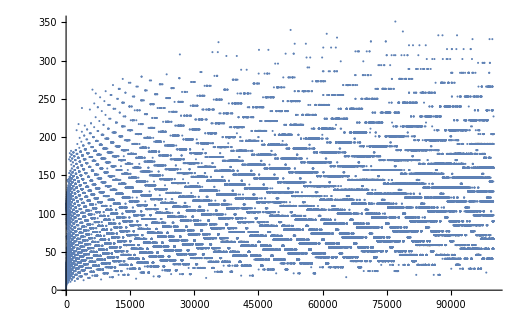

```mathematica
ListPlot[lenList] (* just graphing it for more visualization *)
```

Since all lengths are finite this means that the Collatz Conjecture will most likely reach one for all the numbers since it worked for the first 100 000.

## Are the largest numbers in Collatz sequence generated from prime numbers?

Before starting the project I had a hypothesis that the largest numbers in a Collatz sequence would be generated from prime numbers. In order to prove or disprove this we will find the maximum value of a Collatz sequence generated by the first 1000, 10 000, and 100 000 numbers.

Define a function that gives us the maximum value of a sequence:

```mathematica
colMax[n_]:=Max[colSeq[n]](*here the Max function will return the maximum value of a list*)
```

Now we see if the largest number in the Collatz sequence generated by the first 1000 numbers is generated by a prime number.

```mathematica
maxList=colMax/@Range[1000];(*Creates a list of largest numbers of each Collatz sequence*)
maxVal = Max[maxList] (*save this maximum value*)
maxPosition = Position[maxList,Max[maxList]] (*this will give us the number that generated the largest number by checking what position in the list this number is*)
```

In this case two numbers generated the largest number which is 250 504. And it is generated by 703 and 937. To make sure that this function is giving us the right generators for the maximum value we will try the following:

```mathematica
colMax[703]
colMax[937]
```

This shows that our function works and finds the right generators for the maximum value. Now we check if those values are prime or not.

```mathematica
PrimeQ[703]
PrimeQ[937]
```

By checking we see that one of the numbers if prime one is not. This is non conclusive proof to my claim that the largest numbers are generated by primes so we will try the same thing but for the first 10 000 numbers.

```mathematica
maxList=colMax/@Range[10000];(*Creates a list of largest numbers of each Collatz sequence*)
maxVal = Max[maxList] (*save this maximum value*)
maxPosition = Position[maxList,Max[maxList]] (*this will give us the number that generated the largest number by checking what position in the list this number is*)
```

27114424

{{9663}}

In this case the largest is 9663. Let’s check if this number is prime.

```mathematica
PrimeQ[9663]
```

False

As we see in this case we only have one number that generated the max value and this number was not prime so it seems like I might be disproving my claim that the largest numbers are generated by primes. To make sure we try the same thing for the first 100 000 numbers.

```mathematica
maxList=colMax/@Range[100000];(*Creates a list of largest numbers of each Collatz sequence*)
maxVal = Max[maxList] (*save this maximum value*)
maxPosition = Position[maxList,Max[maxList]] (*this will give us the number that generated the largest number by checking what position in the list this number is*)
```

1570824736

{{77671}}

In this case the largest number is generated by the number 77671. Let’s check if this is prime:

```mathematica
PrimeQ[77671]
```

False

And this number is not prime either. While this is not conclusive proof that the largest numbers are generated by non-prime numbers it shows that my original hypothesis that the largest numbers are generated by primes is false.

## Conclusion:

One thing that we are confident about is that the sequence will always reach 1 since we tried it on 100 000 sequences and they all ended. 

My second claim that the largest numbers in a sequence are generated from a sequence that started with a prime is false. As numbers got larger from 1000 to 10 000 to 100 000 the largest numbers were generated by non-prime numbers. Thus my hypothesis in the beginning was wrong.

## Extra:

In my quest to find out how to generate large numbers I created a graph. In this graph we can see lines that grow faster than others but on the other hand we see lone dots that are as large as the numbers in those lines. So I don’t think that following those lines that are rapidly increasing will give us the largest number in a Collatz sequence since there are lone numbers that are as large if not larger that the numbers in lines

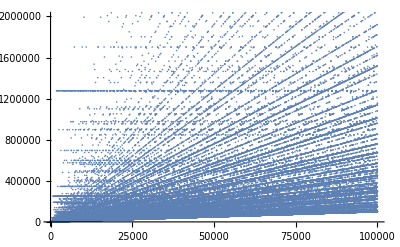

```mathematica
ListPlot[maxList,PlotRange->{0,2000000}]
```

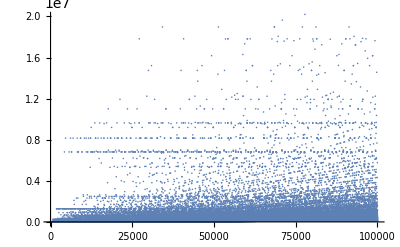

```mathematica
ListPlot[maxList,PlotRange->{0,20000000}]
```

From the second graph we see that the lines take you to a certain point but points that seem to be out of those lines are much larger than the numbers that are part of a line.